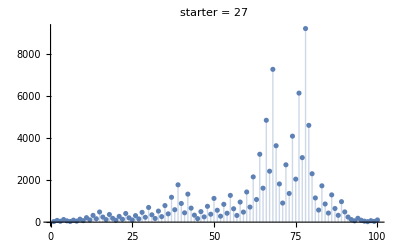

```mathematica
range=100;
starter=27;
data=Table[starter,range];
For[n=starter;i=2,i≤range,i++,If[OddQ[n],n=3 n+1,n=n/2];data⟦i⟧=n];
ListPlot[data,PlotRange->All,Filling->Axis,PlotLabel->"starter = "<>ToString[starter]]
```